# 陷波滤波器（Notch Filter）

## 1. 陷波器参数

采样频率

```mathematica
Fs=21000;
```

滤波器陷波点频率(Hz)

```mathematica
fc=300;
wc=2*Pi*fc;
```

滤波器谐振点3dB带宽(Hz)

```mathematica
fBand=30;
wB=2*Pi*fBand;
```

## 2. 陷波器传函

陷波器连续传函如下

(360000 π^2+s^2)/(360000 π^2+60 π s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s113600003600001FalseFalseFalseAutomaticNoneAutomatic

(3.553057584×10^6+s^2)/(3.553057584×10^6+188.4955592 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s113.5530575843921691027804168e63.5530575843921691027804168e61FalseFalseFalseAutomaticNoneAutomatic

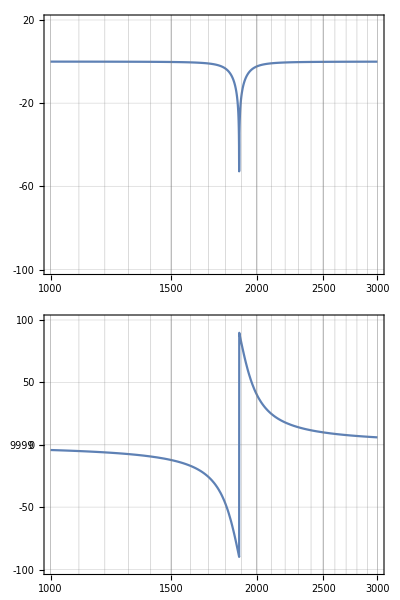

```mathematica
TFNotchFilter = TransferFunctionModel[(s^2 + wc^2)/(s^2 + s*wB + wc^2), s]
N[TFNotchFilter, 10]
BodePlot[TFNotchFilter,{1000, 3000},PlotRange->{{-100,20},{-100,100}},GridLines -> Automatic, ImageSize -> Medium]
```

## 3. 陷波器离散化

陷波器离散传函

```mathematica
TFZNotchFilter=ToDiscreteTimeModel[TFNotchFilter,1/Fs,z,Method->{"BilinearTransform"}]
N[TFZNotchFilter,10]
```

(4900+π^2-9800 z+2 π^2 z+4900 z^2+π^2 z^2)/(4900-7 π+π^2-9800 z+2 π^2 z+4900 z^2+7 π z^2+π^2 z^2)1/21000TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11122512251FalseFalseFalseAutomaticNoneAutomatic

(1. (4909.869604-9780.260791 z+4909.869604 z^2))/(4887.878456-9780.260791 z+4931.860753 z^2)0.00004761904762TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111225.1225.1FalseFalseFalseAutomaticNoneAutomatic

离散陷波器bode图如下

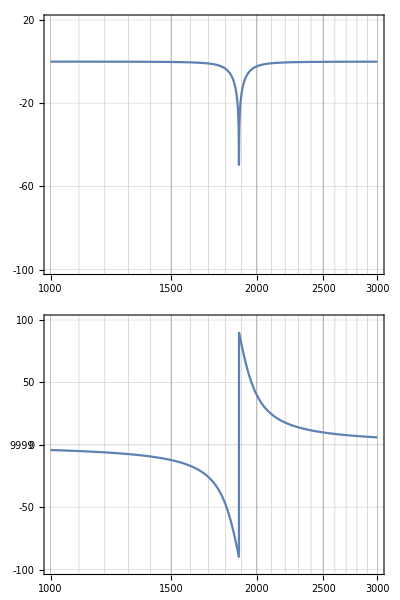

```mathematica
BodePlot[TFZNotchFilter,{1000, 3000},PlotRange->{{-100,20},{-100,100}},GridLines->Automatic,ImageSize->Medium]
```